```mathematica
k=8.617 *(10^(-5));
T=300;
ej=0.00048
```

0.00048

```mathematica
Sum[(2*j +1)*Exp[-j*(j+1)*ej/(k*T)],{j,0,18}]
```

54.1257

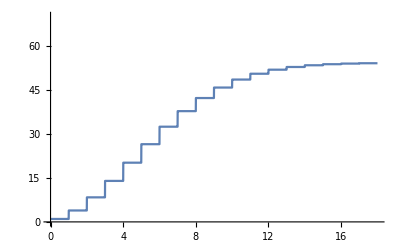
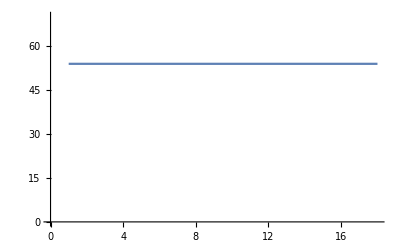

```mathematica
Overlay[{Plot[Sum[(2*j +1)*Exp[-j*(j+1)*ej/(k*T)],{j,0,jf}],{jf,0,18},PlotRange->{{0,18},{0,70}}],ListLinePlot[{{1,53.86},{18,53.86}},PlotRange->{{0,18},{0,70}}]}]
```